```mathematica
alphaRod = 0.4;
alphaSheet = 0.02;
epsilon = 0.1;
diffConst[x_]:=Piecewise[{{alphaSheet, x < 0.5-epsilon},{alphaRod,x ≥ 0.5-epsilon && x < 0.5 + epsilon},{alphaSheet,x≥0.5+epsilon}}];
initF[x_,y_]:= 20*x^2*(x-1)^2*y^2*(y-1)^2; 
systemWithRod = NDSolveValue[{D[u[x,y,t],t]-diffConst[x]*Laplacian[u[x,y,t],{x,y}]==0,DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,1},{y,0,1},{t,0,10}];
systemNoRod = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==0,DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,1},{y,0,1},{t,0,10}];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
Manipulate[Plot3D[{systemNoRod[x,y,t],systemWithRod[x,y,t],0,0.08},{x,0,1},{y,0,1},PlotLegends->{"System without Rod","System with Rod","Zero","Const"}],{t,0,10}]
```

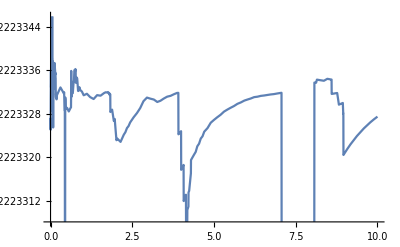

```mathematica
(*This integrates the temperature over the whole interval (0,1)x(0,1) to obtain total energy. 
It then plots that as a function of time.
As can be observed, the total energy is practically constant, as the standard deviation appears to be around 1e-5, 
which can likely be attributed to numerical imprecision error*)
energyRodSys[t_]:=Integrate[systemWithRod[x,y,t],{x,0,1},{y,0,1}];
Plot[energyRodSys[t],{t,0,10}]
```

```mathematica
(*This shows the temperature flow of the system as a function of x at each time point. 
At x=0.4 at x=0.6, which is the boundary between the different diffusion coefficients,
	there is no jump in temperature flow, thus the neumann conditions match*)
tempFlowRodSysX[x_,y_,t_]:=D[systemWithRod[xx,yy,tt],xx]/.{xx->x,yy->y,tt->t};
tempFlowRodSysY[x_,y_,t_]:=D[systemWithRod[xx,yy,tt],yy]/.{xx->x,yy->y,tt->t};
Manipulate[Plot3D[{tempFlowRodSysX[x,y,t],tempFlowRodSysY[x,y,t],1,-1},{x,0.3,0.7},{y,0,1}],{t,0,10}]
```

```mathematica
Manipulate[StreamPlot[{tempFlowRodSysX[x,y,t],tempFlowRodSysY[x,y,t]},{x,0.3,0.7},{y,0,1}],{t,0,10}]
```

```mathematica
Table[StreamPlot[{tempFlowRodSysX[x,y,t],tempFlowRodSysY[x,y,t]},{x,0.3,0.7},{y,0,1}],{t,0,3,0.25}]
```